```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../../ltd_math_utils/ltdTools1.1.m"]
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts 
 ?importGraphs 
 ?getLoopLines 
 ?getCutStructure 
 ?writeMinimalJSON 
 ?extractTensCoeff 
 ?getSymCoeff 
 ?processNumerator 
 ?createSuperGraph 
 ?translateToFeynCalc
 ----------------------------------------- 
 Needs the package FeynCalc which can installed with Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]; InstallFeynCalc[]
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation.

FeynCalc 9.3.0 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

### Export one-loop box with numerators

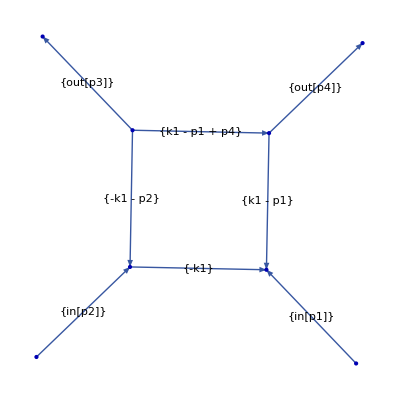

```mathematica
(* get box *)
allGraphs={importGraphs["./phi3graphs.qgr"][[-2]]};
plotGraph[allGraphs,edgeLabels->"momentumMap",plotSize->Scaled[0.2]];
(* set numerator *)
allGraphs[[1,"numerator"]]=SPD[k1,p1];(* FeynCalcNotation!*)
(* get symmetric coefficients. That can be done here or on the fly in the export function *)
allGraphs=getSymCoeff[allGraphs];
fiestaResult=Flatten@ReIm@{5.392921594674065*^-7+6.190910706319407*^-6 ⅈ};
allGraphs=Append[allGraphs,<|"analytical_result_imag"->fiestaResult[[2]],"analytical_result_real"->fiestaResult[[1]]|>];
(* we append the Key and specify on export, that they should be written as well.*)
```

```mathematica
(* set numeric values *)
pp1=SetPrecision[{14,-66/10,-40,0},32];
pp3=SetPrecision[{-43,12,33,0},32];
pp4=SetPrecision[{-28,-50,10,0},32];
pp2=-pp1-pp3-pp4;
kinematics=<|mass[phi]->0,
Thread@Rule[{p1,p2,p3,p4},{1,1,-1,-1}*{pp1,pp2,pp3,pp4}]
|>;
```

```mathematica
(* export *)
```

```mathematica
writeMinimalJSON[allGraphs,kinematics,exportDirectory->"./",processName->"box_Lin_Test",writeNumerator->True,additionalKeys->{"analytical_result_imag","analytical_result_real"}]
Print["done"]
```